Export::errfile: The file E:\Users\Almanzor\Documents\Escuela\Biomecanica\Tareas\TiempoVsModuloAceleracion.xlsx (Acceso denegado) could not be accessed.

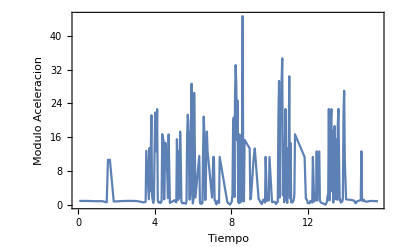

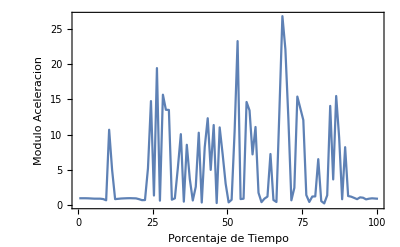

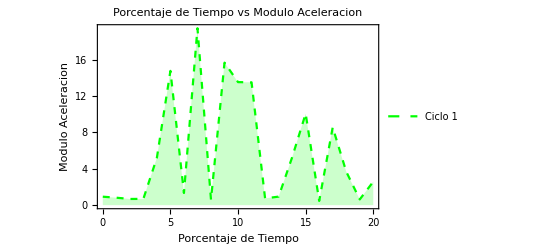

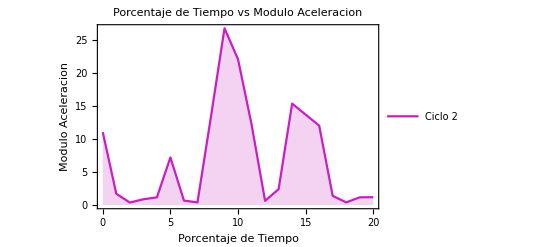

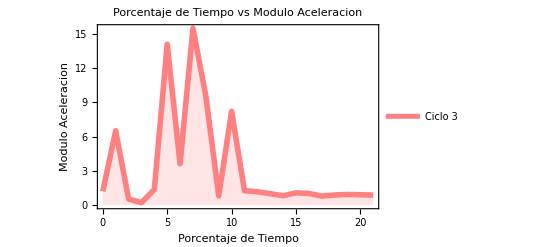

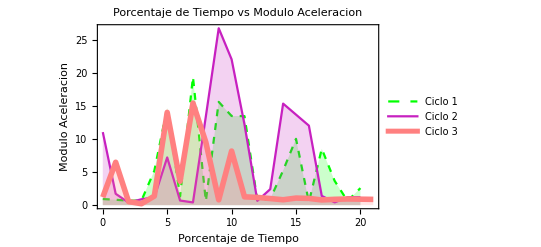

```mathematica
(*Importamos el archivo excel, con las comas cambiadas por puntos*)
e = Import["E:\\Users\\Almanzor\\Documents\\Escuela\\Biomecanica\\Tareas\\touche+acelaracion+1.xlsx"][[1]];
(*Medimos la longitud del arreglo para saber la duracion de los ciclos*)
LongitudDeArreglo = Length[e];
(*Separamos cada componente de la aceleracion en vectores, X, Y y Z*)
AceleracionEnX=Table[{e[[i,2]]},{i,2,LongitudDeArreglo}];
AceleracionEnY=Table[{e[[i,3]]},{i,2,LongitudDeArreglo}];
AceleracionEnZ=Table[{e[[i,4]]},{i,2,LongitudDeArreglo}];
(*Tambien extraigo el vector tiempo*)
Tiempo =Table[{e[[i,1]]},{i,2,LongitudDeArreglo}];
(*Junto cada componente de la aceleracion en un vector*)
VectorAceleracion = Table[{AceleracionEnX[[i,1]],AceleracionEnY[[i,1]],AceleracionEnZ[[i,1]]},{i,1,LongitudDeArreglo-1}];
(*Calculo el modulo del vector aceleracion, y lo guardo en una tabla*)

ModuloDeAceleracion = Table[{Norm[VectorAceleracion[[i]]]},{i,1,LongitudDeArreglo-1}];
(*Hago una tabla con dos datos el tiempo y el modulo de la aceleracion*)
TiempoVsModuloAceleracion = Table[{Tiempo[[i,1]],ModuloDeAceleracion[[i,1]]},{i,1,LongitudDeArreglo-1}];
(*Exporto la tabla con dos datos el tiempo y el modulo de la aceleracion*)
Export["E:\\Users\\Almanzor\\Documents\\Escuela\\Biomecanica\\Tareas\\TiempoVsModuloAceleracion.xlsx",TiempoVsModuloAceleracion];
(*Grafico el tiempo vs el modulo de la aceleracion*)
ListPlot[TiempoVsModuloAceleracion ,Joined->True,Frame->True,FrameLabel->{"Tiempo","Modulo Aceleracion"}]
(*Vamos a graficar como si el movimiento fuera de 0 a 100 para eso calculamos el incremento
con la cantidad final del tiempo menos la inicial entre 100*)
Incremento=(e[[LongitudDeArreglo,1]]-e[[2,1]])/100;
(*La interpolacion crea una funcion de la variable TiempoVsModuloAceleracion en la que podemos evaluar la variable*)
PorcentajeDeTiempoVsModuloAceleracion = Interpolation[TiempoVsModuloAceleracion,InterpolationOrder->1];
(*Armamos una tabla nueva con el eje x en porcentaje y el eje Y con la funcion de interpolacion*)
TablaPorcentajeDeTiempoVsModuloAceleracion =Table[{(i/Incremento),PorcentajeDeTiempoVsModuloAceleracion[i]},{i,TiempoVsModuloAceleracion[[1,1]],TiempoVsModuloAceleracion[[LongitudDeArreglo-1,1]],Incremento}];
(*Graficamos la nueva tabla*)
ListPlot[{TablaPorcentajeDeTiempoVsModuloAceleracion},Joined->True,Frame->True,FrameLabel->{"Porcentaje de Tiempo","Modulo Aceleracion"}]
(*Armamos el primer ciclo 1 con la funcion de interpolacion en el rango que elijamos*)
Ciclo1Completo=Table[{TablaPorcentajeDeTiempoVsModuloAceleracion[[i,1]]-19.423076923076923,TablaPorcentajeDeTiempoVsModuloAceleracion[[i,2]]},{i,20,40,1}];
(*Armamos el primer ciclo 1 con la funcion de interpolacion en el rango que elijamos*)
Ciclo2Completo = Table[{TablaPorcentajeDeTiempoVsModuloAceleracion[[i,1]]-59.423076923076934,TablaPorcentajeDeTiempoVsModuloAceleracion[[i,2]]},{i,60,80,1}];
(*Armamos el primer ciclo 1 con la funcion de interpolacion en el rango que elijamos*)
Ciclo3Completo = Table[{TablaPorcentajeDeTiempoVsModuloAceleracion[[i,1]]-79.42307692307693,TablaPorcentajeDeTiempoVsModuloAceleracion[[i,2]]},{i,80,101,1}];
(*Graficamos el Ciclo 1*)
GraficaCiclo1Completo=ListPlot[{Ciclo1Completo},Joined->True,Filling->Axis,PlotStyle->{{Green,Glow,Dashed}},Frame->True,FrameLabel->{"Porcentaje de Tiempo","Modulo Aceleracion"},PlotLegends->{"Ciclo 1"},PlotLabel->"Porcentaje de Tiempo vs Modulo Aceleracion"]
(*Graficamos el Ciclo 2*)
GraficaCiclo2Completo=ListPlot[{Ciclo2Completo},Joined->True,Filling->Axis,PlotStyle->{{Purple,Glow,Hue[0.84,0.84,0.78]}},Frame->True,FrameLabel->{"Porcentaje de Tiempo","Modulo Aceleracion"},PlotLegends->{"Ciclo 2"},PlotLabel->"Porcentaje de Tiempo vs Modulo Aceleracion"]
(*Graficamos el Ciclo 3*)
GraficaCiclo3Completo=ListPlot[{Ciclo3Completo},Joined->True,Filling->Axis,PlotStyle->{{Pink,Glow,Thickness[0.01]}},Frame->True,FrameLabel->{"Porcentaje de Tiempo","Modulo Aceleracion"},PlotLegends->{"Ciclo 3"},PlotLabel->"Porcentaje de Tiempo vs Modulo Aceleracion"]
(*Graficamos los tres Ciclos en una sola grafica*)

Show[{GraficaCiclo1Completo,GraficaCiclo2Completo,GraficaCiclo3Completo},PlotRange->All]
```